# Metabolic niche model

```mathematica
ClearAll["Global`*"];
ft=Flatten;
fs=FullSimplify;
mx=MatrixForm;
ff=First;



monogeno=Tuples[{Range[0,1],Range[0,1]}];

divloci={1,2};
L=Length[divloci];

locus1=1;
locus2=2;

Dini=-0.12
frequencies = {0.501,0.501};
(*monogeno={{0,0,0,0,0},{0,0,0,0,1},{1,0,0,0,0},{1,0,0,0,1}}*)

polygeno = Flatten[Table[Table[Sort[{monogeno[[i]],monogeno[[j]]}],{j,i,Length[monogeno]}],{i,1,Length[monogeno]}],1]

sig=0.0;
params = {β0->2,b->4,d->1,q->1,cc->1,σ->sig,γ->2,k0->1, k1->0.95,k2->0.6};


recparams[x_,y_,z_]:={ σ->x,k1->y, k2->z ,params}//ft
```

-0.12

{{{0,0},{0,0}},{{0,0},{0,1}},{{0,0},{1,0}},{{0,0},{1,1}},{{0,1},{0,1}},{{0,1},{1,0}},{{0,1},{1,1}},{{1,0},{1,0}},{{1,0},{1,1}},{{1,1},{1,1}}}

β : transmission rate
b : birth rate s
d : death rate s and i
q : [0, 1] cost of infection of poly relative to mono
γ : recovery rate 
σ : recombination rate
k_i : COST upon co-colonization if allele on locus i is shared (positive: assortative ; negative : disassortative)
m : benefit of advantageous allele
cc : efficiency of co-colonization relative to primary colonization

#### all multiplicative

```mathematica
n=Length[monogeno[[1]]]; (* number of genes *)
β[i_,j_] := If[j===0,Subscript[β, mono][i],Subscript[β, co][i,j]]
```

```mathematica
Subscript[β, mono][i_] := β0 
Subscript[β, co][i_,j_]:=cc (β0 * Subscript[K, metabo][i,j])  (*i infects already j*)


Subscript[K, metabo][i_,j_] :=  If[i[[1]]==j[[1]] ,If[i[[2]]==j[[2]] ,k2,k1],If[i[[2]]==j[[2]] ,k1,k0]]





sort[i_,j_]:= Sort[{i,j}]  (* to insure that using Subscript[i, i,j] is the same is Subscript[i, j,i]*)


δsame[i_,j_] := If[i==j,1,0]

(*Subscript[p, rec][i_,j_,l_] :=Sum[If[ (Delete[i,X]== Delete[l,X]) && j[[X]]==l[[X]],1/n,0],{X,1,n}]*) (* proba that i recombines with j to form l*) (*for now recombination of i with j gives : i but at one random position (all equally likely) its the allele of j*)    (*BENEF UNABLE TO RECOMBINE*)
Subscript[p, rec][i_,j_,l_] :=Sum[If[ (Delete[i,X]== Delete[l,X]) && j[[X]]==l[[X]],1/L,0],{X,divloci}]

irec[i_,j_,X_]:=ReplacePart[i,X->j[[X]]]
```

```mathematica
β[{0,0},0]
β[{1,1},0]
β[{0,0},{0,1}]
β[{1,1},{1,1}]
```

β0

β0

cc k1 β0

cc k2 β0

```mathematica
eqmono=Table[Subscript[ℐ, i]'[t] == (β[i,0]  Subscript[ℐ, i][t])s[t]  (* + mono infects s*)

- Subscript[ℐ, i][t](d+γ)(* - death+recovery*)

-Subscript[ℐ, i][t] Sum[ (Subscript[ℐ, j][t]  β[j,i]),{j,monogeno}](* - mono infects mono*)

+ γ( Sum[Subscript[ℐ, sort[i,j]][t] ,{j,monogeno}] + Subscript[ℐ, sort[i,i]][t])(* + recovery of poly*)

+ s[t](1-σ) Sum[Subscript[ℐ, sort[i,j]][t] β[i,0] q (1+δsame[i,j]),{j,monogeno}] (*poly infects s*) (* no recombi*)

-  Subscript[ℐ, i][t] q (1-σ)Sum[Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t] (β[ij[[1]],i]+β[ij[[2]],i]),{ij,polygeno}] (* - poly infects mono*) (* no recombi*)

-  Subscript[ℐ, i][t] q σ Sum[1/L Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t]  β[irec[lm[[1]],lm[[2]],nrec],i] +  Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t]  β[irec[lm[[2]],lm[[1]],nrec],i] ,{nrec,divloci}],{lm,polygeno}] (* - poly infects mono*) (* RECOMBI*)

+ σ s[t] β[i,0] q Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t] (Subscript[p, rec][lm[[1]],lm[[2]],i]+Subscript[p, rec][lm[[2]],lm[[1]],i]),{lm,polygeno}](*poly infects s*) (* recombi*)


,{i,monogeno}];


eqpoly = Table[Subscript[ℐ, sort[ij[[1]],ij[[2]]]]'[t] ==  Subscript[ℐ, ij[[1]]][t]  Subscript[ℐ, ij[[2]]][t](β[ij[[1]],ij[[2]]] +( 1-δsame[ij[[1]],ij[[2]]]) β[ij[[2]],ij[[1]]])(* + mono infects mono *) 
   
- Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t](d+2γ)(* - death+recovery *)

+Subscript[ℐ, ij[[1]]][t] q  (1-σ)Sum[Subscript[ℐ, sort[ij[[2]],l]][t] β[ij[[2]],ij[[1]]] (1+δsame[ij[[2]],l]),{l,monogeno}] (*poly infects mono1*) (* no recombi*)

+(1-δsame[ij[[1]],ij[[2]]])Subscript[ℐ, ij[[2]]][t] q  (1-σ)Sum[Subscript[ℐ, sort[ij[[1]],l]][t] β[ij[[1]],ij[[2]]] (1+δsame[ij[[1]],l]),{l,monogeno}] (*poly infects mono2 if not same *)(* no recombi*)

+Subscript[ℐ, ij[[1]]][t] q  σ Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t] β[ij[[2]],ij[[1]]]  (Subscript[p, rec][lm[[1]],lm[[2]],ij[[2]]] + Subscript[p, rec][lm[[2]],lm[[1]],ij[[2]]]),{lm,polygeno}] (*poly infects mono1*) (* RECOMBI*)

+(1-δsame[ij[[1]],ij[[2]]])Subscript[ℐ, ij[[2]]][t] q  σ Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t] β[ij[[1]],ij[[2]]]  (Subscript[p, rec][lm[[1]],lm[[2]],ij[[1]]] + Subscript[p, rec][lm[[2]],lm[[1]],ij[[1]]]),{lm,polygeno}] (*poly infects mono1*) (* RECOMBI*)

,{ij,polygeno}];




eqs=s'[t]==b (* + birth*)   -s[t] (Sum[Subscript[ℐ, j][t] β[j,0],{j,monogeno}]) (* - mono infects s*) - s[t]d  (* - death*)  + γ (Sum[Subscript[ℐ, j][t],{j,monogeno}])  (* + recovery of mono *)- s[t] (1-σ) Sum[Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t] q (β[ij[[1]],0] + β[ij[[2]],0]),{ij,polygeno}] (* - poly infects s*) (*no recombi*)- s[t] σ 1/L Sum[Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t] q Sum[β[irec[ij[[1]],ij[[2]],X],0] +β[irec[ij[[2]],ij[[1]],X],0] ,{X,divloci}],{ij,polygeno}] (* - poly infects s*) (*recombi*);




eq=  {eqs,eqmono,eqpoly}//ft;


Total[eq[[All,2]]]- b+d(s[t]+Sum[Subscript[ℐ, j][t],{j,monogeno}]+Sum[Subscript[ℐ, j][t],{j,polygeno}])//fs    (*THE ABOVE TAKES A REALLY LONG TIME, USED TO CHECK IF SYSTEM IS GOOD. ONE CAN CHECK WITH THREE LOCI IN UNDER A MINUTE*)
```

0

```mathematica
temps=5000;



inits = {s[0]==b /d};
initpoly=ft[{Table[Subscript[ℐ, k][0] ==0,{k,polygeno}]}];


initmono=ft[Table[Subscript[ℐ, k][0] == 1 *Product[If[k[[X]]==1,frequencies[[X]],1-frequencies[[X]]], {X,divloci}]+ Dini If[k[[locus1]] == k[[locus2]],1,-1],{k,monogeno}]]; (*all monos + jitter*)
initmonoDtemp=ft[Table[Subscript[ℐ, k][0] == 1 *Product[If[k[[X]]==1,frequencies[[X]],1-frequencies[[X]]], {X,divloci}]+ Dtemp If[k[[locus1]] == k[[locus2]],1,-1],{k,monogeno}]]; (*all monos + jitter*)
(*initmono={Subscript[ℐ, {0,0,0,0,0}][0]==0.4,Subscript[ℐ, {0,0,0,0,1}][0]==0.1,Subscript[ℐ, {0,0,0,1,0}][0]==0.1,Subscript[ℐ, {0,0,0,1,1}][0]==0.4};*)


init={inits,initpoly,initmono}//ft
initDtemp={inits,initpoly,initmonoDtemp}//ft

vars = {s[t],Table[Subscript[ℐ, j][t],{j,monogeno}],Table[Subscript[ℐ, j][t],{j,polygeno}]}//ft;


sol=NDSolve[{eq//.params,init//.params}//ft,vars,{t,0,temps},MaxStepSize->0.1];

(*Plot[Subscript[ℐ, {0,0,0,0,0}][t]/.sol,{t,0,temps}, PlotRange->All];*)

recsol[x_,y_,z_,Dtempi_]:=NDSolve[{eq//.recparams[x,y,z],initDtemp/.Dtemp->Dtempi//.recparams[x,y,z]}//ft,vars,{t,0,temps},MaxStepSize->0.1];
```

{s[0]==b/d,ℐ_{{0,0},{0,0}}[0]==0,ℐ_{{0,0},{0,1}}[0]==0,ℐ_{{0,0},{1,0}}[0]==0,ℐ_{{0,0},{1,1}}[0]==0,ℐ_{{0,1},{0,1}}[0]==0,ℐ_{{0,1},{1,0}}[0]==0,ℐ_{{0,1},{1,1}}[0]==0,ℐ_{{1,0},{1,0}}[0]==0,ℐ_{{1,0},{1,1}}[0]==0,ℐ_{{1,1},{1,1}}[0]==0,ℐ_{0,0}[0]==0.129001,ℐ_{0,1}[0]==0.369999,ℐ_{1,0}[0]==0.369999,ℐ_{1,1}[0]==0.131001}

{s[0]==b/d,ℐ_{{0,0},{0,0}}[0]==0,ℐ_{{0,0},{0,1}}[0]==0,ℐ_{{0,0},{1,0}}[0]==0,ℐ_{{0,0},{1,1}}[0]==0,ℐ_{{0,1},{0,1}}[0]==0,ℐ_{{0,1},{1,0}}[0]==0,ℐ_{{0,1},{1,1}}[0]==0,ℐ_{{1,0},{1,0}}[0]==0,ℐ_{{1,0},{1,1}}[0]==0,ℐ_{{1,1},{1,1}}[0]==0,ℐ_{0,0}[0]==0.249001+Dtemp,ℐ_{0,1}[0]==0.249999-Dtemp,ℐ_{1,0}[0]==0.249999-Dtemp,ℐ_{1,1}[0]==0.251001+Dtemp}

```mathematica
init//.params
```

{s[0]==4,ℐ_{{0,0},{0,0}}[0]==0,ℐ_{{0,0},{0,1}}[0]==0,ℐ_{{0,0},{1,0}}[0]==0,ℐ_{{0,0},{1,1}}[0]==0,ℐ_{{0,1},{0,1}}[0]==0,ℐ_{{0,1},{1,0}}[0]==0,ℐ_{{0,1},{1,1}}[0]==0,ℐ_{{1,0},{1,0}}[0]==0,ℐ_{{1,0},{1,1}}[0]==0,ℐ_{{1,1},{1,1}}[0]==0,ℐ_{0,0}[0]==0.129001,ℐ_{0,1}[0]==0.369999,ℐ_{1,0}[0]==0.369999,ℐ_{1,1}[0]==0.131001}

{RGBColor[0.9882352941176471, 0.5098039215686274, 0.49411764705882355],RGBColor[0.6823529411764706, 0.803921568627451, 0.8823529411764706],RGBColor[0.23529411764705882, 0.4627450980392157, 0.6862745098039216],RGBColor[0.9294117647058824, 0.21568627450980393, 0.19607843137254902]}

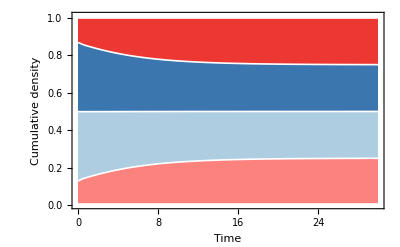

```mathematica
tabletoplot={0.005,Table[Total[Table[((Evaluate[(Subscript[ℐ, g][t] + Sum[Subscript[ℐ, sort[g,j]][t],{j,monogeno}]+Subscript[ℐ, sort[g,g]][t]  )]/.sol//ff) / (Sum[(Evaluate[(Subscript[ℐ, gt][t] + Sum[Subscript[ℐ, sort[gt,j]][t],{j,monogeno}]+Subscript[ℐ, sort[gt,gt]][t]  )]/.sol//ff),{gt,monogeno}]))/.t->y,{g,monogeno}][[1;;x]]//ft],{x,1,4}]}//ft;
colsMuller=RGBColor/@{"#fc827e","#AECDE1","#3C76AF","#ed3732"}
Plot[Evaluate@tabletoplot,{y,0,30}, PlotRange->{All,{0,1.01}}, PlotPoints->10, MaxRecursion->4, PlotStyle->Directive[White,Thickness@0.003], Filling->{1->{{2},colsMuller[[1]]}, 2->{{3},colsMuller[[2]]}, 3->{{4},colsMuller[[3]]}, 4->{{5},colsMuller[[4]]}}, Frame->{{True, False},{True,False}}, AxesOrigin->{0,0}, FrameLabel->{{Style["Cumulative density",15,Black],""},{Style["Time",15,Black],""}}, PlotRangePadding->None]
```

heatmap for presence in co - colonisation

in the whole pop

```mathematica
eqth=Thread[eq[[All,1]]->eq[[All,2]]];
```

```mathematica
denstot[t_]= Sum[(Subscript[ℐ, x][t]),{x,monogeno}]+ 2Sum[(Subscript[ℐ, x][t]),{x,polygeno}]

Subscript[dens, AB][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==1,1,0]*If[x[[locus2]]==1,1,0],{x,monogeno}]+ Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==1,1,0]*If[y[[1]][[locus2]]==1,1,0]+If[y[[2]][[locus1]]==1,1,0]*If[y[[2]][[locus2]]==1,1,0]),{y,polygeno}];
Subscript[dens, Ab][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==1,1,0]*If[x[[locus2]]==0,1,0],{x,monogeno}]+ Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==1,1,0]*If[y[[1]][[locus2]]==0,1,0]+If[y[[2]][[locus1]]==1,1,0]*If[y[[2]][[locus2]]==0,1,0]),{y,polygeno}];
Subscript[dens, aB][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==0,1,0]*If[x[[locus2]]==1,1,0],{x,monogeno}]+ Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==0,1,0]*If[y[[1]][[locus2]]==1,1,0]+If[y[[2]][[locus1]]==0,1,0]*If[y[[2]][[locus2]]==1,1,0]),{y,polygeno}];
Subscript[dens, ab][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==0,1,0]*If[x[[locus2]]==0,1,0],{x,monogeno}]+ Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==0,1,0]*If[y[[1]][[locus2]]==0,1,0]+If[y[[2]][[locus1]]==0,1,0]*If[y[[2]][[locus2]]==0,1,0]),{y,polygeno}];

Subscript[qdens, AB][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==1,1,0]*If[x[[locus2]]==1,1,0],{x,monogeno}]+ q Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==1,1,0]*If[y[[1]][[locus2]]==1,1,0]+If[y[[2]][[locus1]]==1,1,0]*If[y[[2]][[locus2]]==1,1,0]),{y,polygeno}];
Subscript[qdens, Ab][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==1,1,0]*If[x[[locus2]]==0,1,0],{x,monogeno}]+ q Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==1,1,0]*If[y[[1]][[locus2]]==0,1,0]+If[y[[2]][[locus1]]==1,1,0]*If[y[[2]][[locus2]]==0,1,0]),{y,polygeno}];
Subscript[qdens, aB][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==0,1,0]*If[x[[locus2]]==1,1,0],{x,monogeno}]+ q Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==0,1,0]*If[y[[1]][[locus2]]==1,1,0]+If[y[[2]][[locus1]]==0,1,0]*If[y[[2]][[locus2]]==1,1,0]),{y,polygeno}];
Subscript[qdens, ab][t_]=Sum[(Subscript[ℐ, x][t])*If[x[[locus1]]==0,1,0]*If[x[[locus2]]==0,1,0],{x,monogeno}]+ q Sum[(Subscript[ℐ, y][t])*(If[y[[1]][[locus1]]==0,1,0]*If[y[[1]][[locus2]]==0,1,0]+If[y[[2]][[locus1]]==0,1,0]*If[y[[2]][[locus2]]==0,1,0]),{y,polygeno}];

Subscript[H, ab][t] = s[t]+k2 Subscript[ℐ, {0,0}][t]+k0 Subscript[ℐ, {1,1}][t]+k1 (Subscript[ℐ, {0,1}][t]+Subscript[ℐ, {1,0}][t]);(*rate of new infection per capita*)
Subscript[H, aB][t] = s[t]+k2 Subscript[ℐ, {0,1}][t]+k0 Subscript[ℐ, {1,0}][t]+k1 (Subscript[ℐ, {0,0}][t]+Subscript[ℐ, {1,1}][t]);
Subscript[H, Ab][t] = s[t]+k2 Subscript[ℐ, {1,0}][t]+k0 Subscript[ℐ, {0,1}][t]+k1 (Subscript[ℐ, {0,0}][t]+Subscript[ℐ, {1,1}][t]);
Subscript[H, AB][t] = s[t]+k2 Subscript[ℐ, {1,1}][t]+k0 Subscript[ℐ, {0,0}][t]+k1 (Subscript[ℐ, {0,1}][t]+Subscript[ℐ, {1,0}][t]);

Subscript[fgene, A][t_] =( Subscript[dens, AB][t]+Subscript[dens, Ab][t])/denstot[t];
Subscript[fgene, B][t_] =( Subscript[dens, AB][t]+Subscript[dens, aB][t])/denstot[t];
Subscript[fstrain, AB][t_] =( Subscript[dens, AB][t])/denstot[t];
Subscript[fstrain, ab][t_] =( Subscript[dens, ab][t])/denstot[t];
Subscript[fstrain, Ab][t_] =( Subscript[dens, Ab][t])/denstot[t];
Subscript[fstrain, aB][t_] =( Subscript[dens, aB][t])/denstot[t];


Subscript[s, A][t_] = (D[Subscript[dens, Ab][t],t] / Subscript[dens, Ab][t])-((D[Subscript[dens, ab][t],t] / Subscript[dens, ab][t]));
Subscript[s, B][t_] = (D[Subscript[dens, aB][t],t] / Subscript[dens, aB][t])-((D[Subscript[dens, ab][t],t] / Subscript[dens, ab][t]));
Subscript[s, AB][t_] = (D[Subscript[dens, AB][t],t] / Subscript[dens, AB][t])+((D[Subscript[dens, ab][t],t] / Subscript[dens, ab][t])) - ((D[Subscript[dens, Ab][t],t] / Subscript[dens, Ab][t])-((D[Subscript[dens, aB][t],t] / Subscript[dens, aB][t])));
ss[t_]= Subscript[s, A][t]Subscript[fgene, A][t]+Subscript[s, B][t]Subscript[fgene, B][t]+Subscript[s, AB][t]Subscript[fstrain, AB][t];

DD[t_] = Subscript[fstrain, AB][t] - (Subscript[fgene, A][t] Subscript[fgene, B][t])/.eqth//.params;
DDD[t_]=Evaluate[D[DD[t],t]]/.eqth//.params;

Subscript[Dfgene, A][t_]=Evaluate[D[Subscript[fgene, A][t],t]]/.eqth//.params;
Subscript[Dfgene, B][t_]=Evaluate[D[Subscript[fgene, B][t],t]]/.eqth//.params;
DDD[t_]=Evaluate[D[DD[t],t]]/.eqth//.params;


Subscript[r, ab][t_] = D[Subscript[dens, ab][t],t] / Subscript[dens, ab][t];
Subscript[r, Ab][t_] = D[Subscript[dens, Ab][t],t] / Subscript[dens, Ab][t];
Subscript[r, aB][t_] = D[Subscript[dens, aB][t],t] / Subscript[dens, aB][t];
Subscript[r, AB][t_] = D[Subscript[dens, AB][t],t] / Subscript[dens, AB][t];


negDmax[t_] := DD[t]/Max[{-Subscript[fgene, A][t]Subscript[fgene, B][t], -(1-Subscript[fgene, A][t])(1-Subscript[fgene, B][t])}];
posDmax[t_] :=DD[t]/ Min[{Subscript[fgene, A][t](1-Subscript[fgene, B][t]), Subscript[fgene, A][t](1-Subscript[fgene, B][t])}];

SuperStar[D][t_] := If[DD[t]>0,posDmax[t],negDmax[t]]
```

ℐ_{0,0}[t]+ℐ_{0,1}[t]+ℐ_{1,0}[t]+ℐ_{1,1}[t]+2 (ℐ_{{0,0},{0,0}}[t]+ℐ_{{0,0},{0,1}}[t]+ℐ_{{0,0},{1,0}}[t]+ℐ_{{0,0},{1,1}}[t]+ℐ_{{0,1},{0,1}}[t]+ℐ_{{0,1},{1,0}}[t]+ℐ_{{0,1},{1,1}}[t]+ℐ_{{1,0},{1,0}}[t]+ℐ_{{1,0},{1,1}}[t]+ℐ_{{1,1},{1,1}}[t])

### expression of epistasis

```mathematica
Subscript[s, AB][t] = Subscript[r, AB][t]+Subscript[r, ab][t]-Subscript[r, Ab][t]-Subscript[r, aB][t];
Subscript[s, AB][t]/.eqth/.cc->1/.q->1/.σ->0//fs
(*Subscript[s, AB][t]/.eqth/.cc->1/.q->(1/2)/.σ->0//fs*)
```

(k0-2 k1+k2) β0 (ℐ_{0,0}[t]-ℐ_{0,1}[t]-ℐ_{1,0}[t]+ℐ_{1,1}[t])

```mathematica
(Subscript[s, AB][t]/.eqth/.cc->1/.q->(1/2)/.σ->0)==((β0/2)(-Subscript[H, aB][t] (1+(Subscript[ℐ, {0,1}][t])/(Subscript[dens, aB][t]))-Subscript[H, Ab][t] (1+(Subscript[ℐ, {1,0}][t])/(Subscript[dens, Ab][t]))+Subscript[H, AB][t] (1+(Subscript[ℐ, {1,1}][t])/(Subscript[dens, AB][t]))+Subscript[H, ab][t] (1+(Subscript[ℐ, {0,0}][t])/(Subscript[dens, ab][t]))))//fs
```

True

```mathematica
tmax=temps

ticks01=Table[{i,i},{i,0,1,0.2}];
kmin=0;
kmax=1;
kstep=0.02;


transpa=ListPlot[{{0,0},{1,1}}, Filling->Bottom,Joined->True, FillingStyle->Opacity[1,White], PlotStyle->Opacity[0.5,Gray]];
```

5000

## Figure 2 and S3

{RGBColor[0.054901960784313725, 0.4, 0.5725490196078431],RGBColor[0.35294117647058826, 0.396078431372549, 0.6941176470588235],RGBColor[0.6823529411764706, 0.3215686274509804, 0.6745098039215687],RGBColor[0.9294117647058824, 0.20392156862745098, 0.48627450980392156],RGBColor[1., 0.2901960784313726, 0.1803921568627451]}

Blend::argl: 1/2+v/2 should be a real number or a list of non-negative numbers, which has the same length as {color,color,color,color,color}.

{0,0.02}

{0.1,-0.1}

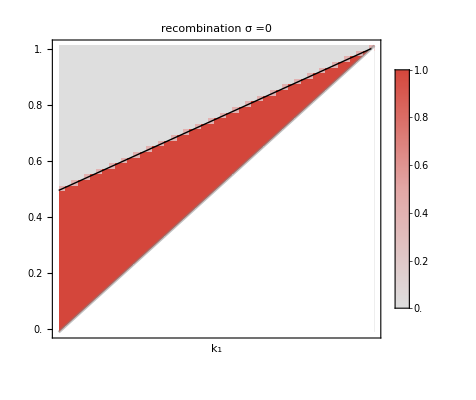

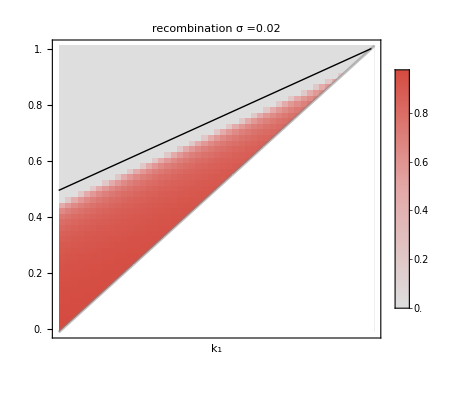

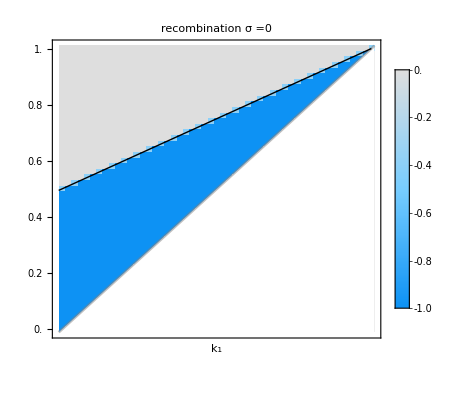

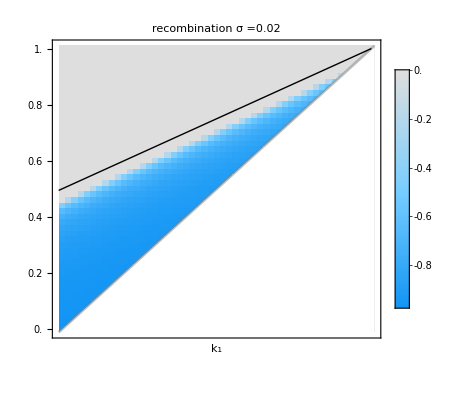

{{Null,Null},{Null,Null}}

1

```mathematica
RGBColor/@{"#0e6692","#5a65b1","#ae52ac","#ed347c","#ff4a2e"}
rainbow[z_]:=Blend[Reverse[{RGBColor["#D4463B"],
RGBColor["#E3A6A5"],
RGBColor["#DEDEDE"],
RGBColor["#77CDFF"],
RGBColor["#0D92F4"]}],z]
col[v_]=Opacity[1,rainbow[Rescale[v,{-01,1}]]];





tempσs={0,0.02}
Dtemps = {0.1,-0.1}

line=Graphics[Line[{{-kstep/2,0.5-kstep/4},{1 ,1}}]];




transpa=ListPlot[{{-kstep/2,-kstep/2},{1+kstep/2,1+kstep/2}}, Filling->Bottom,Joined->True, FillingStyle->Opacity[1,White], PlotStyle->Opacity[0.5,Gray]];



Table[Table[Print[Show[MatrixPlot[Reverse[Replace[Table[
If[k1>=k2,If[(DD[t]/.recsol[tempσ,k1,k2,Dtemp]/.t->tmax//ft//ff)>=0,posDmax[t]/.recsol[tempσ,k1,k2,Dtemp]/.t->tmax//ft//ff,-negDmax[t]/.recsol[tempσ,k1,k2,Dtemp]/.t->tmax//ft//ff]/.Indeterminate->0/.ComplexInfinity->0,0]
,{k1,kmin,kmax,kstep},{k2,kmin,kmax,kstep}],x_?NumericQ:>If[Abs[x]>10,0,x],{2}],1],DataRange->{{0,kmax},{0,kmax}}, PlotLegends->Automatic,PlotLabel->"recombination σ ="<>ToString[tempσ] ,
 PlotLegends->BarLegend[{rainbow[Rescale[#1,{-6,4}]]&,{1,4}}],
ColorFunctionScaling->False, 
ColorFunction->col    , Frame->{{True,False},{False,True}}, PlotRangePadding->None, FrameLabel->{{Style["k_1",14, Black],None},{None,Style["k_2",14, Black]}},FrameTicks->{{ticks01,None},(*left and right y-axes*){None,ticks01}    (*bottom and top x-axes*)},DataRange->{{0,1},{0,1}},PlotRange->All,AspectRatio->1],transpa,line,(*Graphics[{cross[0.4,0.4,0.02],cross[0.4,0.5,0.02],cross[0.4,0.6,0.02]}],*)DataRange->{{0,1},{0,1}},PlotRange->All,AspectRatio->1]],{tempσ,tempσs}],{Dtemp,Dtemps}]

q/.recparams[x,y,z]
```

{0.02}

{0.1}

0.936309

0.890413

0.735717

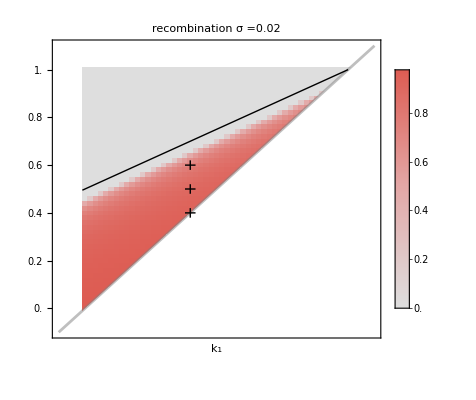

{{Null}}

```mathematica
kstep=0.02;
tempσs={0.02}
Dtemps = {0.1}
line=Graphics[Line[{{-kstep/2,0.5-kstep/4},{1 ,1}}]];
posDmax[t]/.recsol[0.02,0.4,0.4,0.1]/.t->tmax//ft//ff
posDmax[t]/.recsol[0.02,0.5,0.4,0.1]/.t->tmax//ft//ff
posDmax[t]/.recsol[0.02,0.6,0.4,0.1]/.t->tmax//ft//ff

cross[x_,y_,δ_]:={Line[{{x-δ,y},{x+δ,y}}],Line[{{x,y-δ},{x,y+δ}}]};



Table[Table[Print[Show[MatrixPlot[Reverse[Replace[Table[
If[k1>=k2,If[(DD[t]/.recsol[tempσ,k1,k2,Dtemp]/.t->tmax//ft//ff)>=0,posDmax[t]/.recsol[tempσ,k1,k2,Dtemp]/.t->tmax//ft//ff,-negDmax[t]/.recsol[tempσ,k1,k2,Dtemp]/.t->tmax//ft//ff]/.Indeterminate->0/.ComplexInfinity->0,0]
,{k1,kmin,kmax,kstep},{k2,kmin,kmax,kstep}],x_?NumericQ:>If[Abs[x]>10,0,x],{2}],1],DataRange->{{0,kmax},{0,kmax}}, PlotLegends->Automatic,PlotLabel->"recombination σ ="<>ToString[tempσ] ,
 PlotLegends->BarLegend[{rainbow[Rescale[#1,{-6,4}]]&,{1,4}}],
ColorFunctionScaling->False, 
ColorFunction->col    , Frame->{{True,False},{False,True}}, PlotRangePadding->None, FrameLabel->{{Style["k_1",14, Black],None},{None,Style["k_2",14, Black]}},FrameTicks->{{ticks01,None},(*left and right y-axes*){None,ticks01}    (*bottom and top x-axes*)},DataRange->{{0,1},{0,1}},PlotRange->All,AspectRatio->1],transpa,line,Graphics[{cross[0.4,0.4,0.02],cross[0.4,0.5,0.02],cross[0.4,0.6,0.02]}],DataRange->{{0,1},{0,1}},PlotRange->All,AspectRatio->1]],{tempσ,tempσs}],{Dtemp,Dtemps}]
```

## Figure S4

20

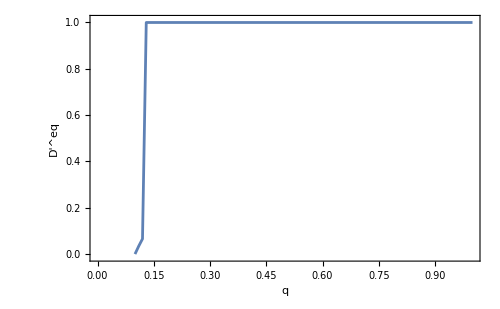

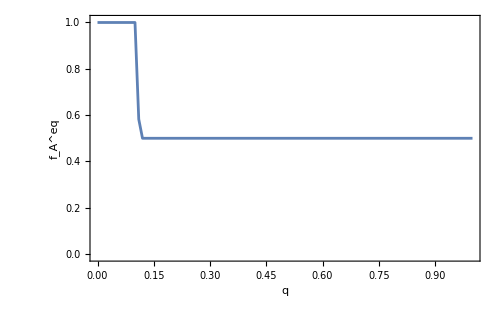

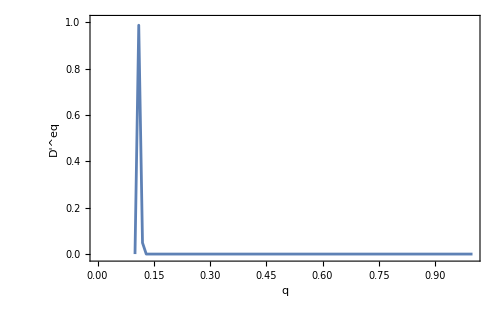

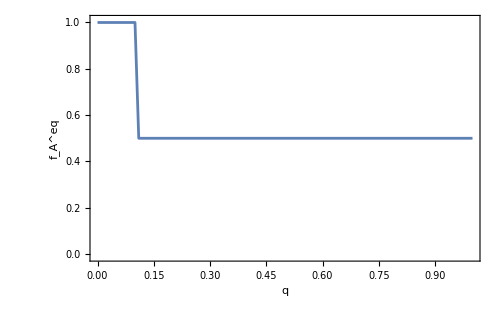

```mathematica
(*Your existing setup code*)qmin=0.1;
qmax=1;
qstep=0.01;
fontsizee=20
qparams[x_,y_,z_,qq_]:={σ->x,k1->y,k2->z,q->qq,params}//ft;
qsol[x_,y_,z_,Dtempi_,qq_]:=NDSolve[{eq//.qparams[x,y,z,qq],initDtemp/. Dtemp->Dtempi//.qparams[x,y,z,qq]}//ft,vars,{t,0,temps},MaxStepSize->0.1];

Dtempi=0.2;

(*First set of parameters:k1=0.6,k2=0.5*)
k1=0.6;
k2=0.5;
data=Table[{q,If[(Abs[DD[t]]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff)<0.001,0,If[(DD[t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff)>=0,posDmax[t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff,-negDmax[t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff]]},{q,qmin,qmax,qstep}];

ListPlot[data,Joined->True,PlotRange->{{0,1},{-0.01,1.01}},FrameLabel->{Style["q",FontSize->fontsizee],Style["D\!\(\*SuperscriptBox[\('\), \(eq\)]\)",FontSize->fontsizee]},Frame->True,FrameStyle->{{Black,None},{Black,None}},(*Left/bottom only*)ImageSize->500  (*Optional:Increase overall plot size*)]

data=Table[{q,(Subscript[fgene,A][t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff)},{q,0,qmax,qstep}];

ListPlot[data,Joined->True,PlotRange->{{0,1},{-0.01,1.01}},FrameLabel->{Style["q",FontSize->fontsizee],Style["\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(A\)], \(eq\)]\)",FontSize->fontsizee]},Frame->True,FrameStyle->{{Black,None},{Black,None}},ImageSize->500]

(*Second set of parameters:k1=0.8,k2=0.5*)
k1=0.8;
k2=0.5;
data=Table[{q,If[(Abs[DD[t]]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff)<0.001,0,If[(DD[t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff)>=0,posDmax[t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff,-negDmax[t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff]]},{q,qmin,qmax,qstep}];

ListPlot[data,Joined->True,PlotRange->{{0,1},{-0.01,1.01}},FrameLabel->{Style["q",FontSize->fontsizee],Style["D\!\(\*SuperscriptBox[\('\), \(eq\)]\)",FontSize->fontsizee]},Frame->True,FrameStyle->{{Black,None},{Black,None}},ImageSize->500]

data=Table[{q,(Subscript[fgene,A][t]/. qsol[0,k1,k2,Dtempi,q]/. t->tmax//ft//ff)},{q,0,qmax,qstep}];

ListPlot[data,Joined->True,PlotRange->{{0,1},{-0.01,1.01}},FrameLabel->{Style["q",FontSize->fontsizee],Style["\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(A\)], \(eq\)]\)",FontSize->fontsizee]},Frame->True,FrameStyle->{{Black,None},{Black,None}},ImageSize->500]
```

## D trajectories

```mathematica
cols=RGBColor/@{"#0e6692","#5a65b1","#ae52ac","#ed347c","#ff4a2e"}

ps1={};
Do[frequencies={0.5,0.5};

inits = {s[0]==b /d};
initpoly=ft[{Table[Subscript[ℐ, k][0] ==0,{k,polygeno}]}];
initmonoD[Dtemp_]=ft[Table[Subscript[ℐ, k][0] == 1 *Product[If[k[[X]]==1,frequencies[[X]],1-frequencies[[X]]] , {X,divloci}]+ Dtemp If[k[[locus1]] == k[[locus2]],1,-1],{k,monogeno}]]; (*all monos + jitter*)
(*initmono={Subscript[ℐ, {0,0,0,0,0}][0]==0.4,Subscript[ℐ, {0,0,0,0,1}][0]==0.1,Subscript[ℐ, {0,0,0,1,0}][0]==0.1,Subscript[ℐ, {0,0,0,1,1}][0]==0.4};*)

initD[Dtemp_]:={inits,initpoly,initmonoD[Dtemp]}//ft;

initsol[Dtemp_]:=NDSolve[{eq//.recparams[σ0,0.5,0.2],initD[Dtemp]//.recparams[σ0,0.5,0.2]}//ft,vars,{t,0,temps},MaxStepSize->0.1]//ft;
tmax=40;
tempsol=.;
listDstart=Range[-0.25,0.25,0.125];
tempsol=ConstantArray[0,Length[listDstart]];

i=1;
Do[tempsol[[i]] = initsol[Dstart];
i=i+1
,{Dstart,listDstart}];



(*Plot[Table[DD[t]/.tempsol[[i]]/.t->x,{i,1,Length[listDstart]}],{x,0,tmax}, PlotRange->All];*)
ps1=AppendTo[ps1,Plot[Evaluate @Table[If[Evaluate[DD[t]/.tempsol[[i]]/.t->x/.params]>0,Evaluate[posDmax[t]/.tempsol[[i]]/.t->x],Evaluate[-negDmax[t]/.tempsol[[i]]/.t->x]],{i,1,Length[listDstart]}],{x,0,tmax}, PlotRange->All, PlotLabel->"k_1=0.5 , k_2=0.2 , recombination σ="<>ToString[σ0], PlotStyle->cols]],{σ0,{0,0.02}}]
```

{RGBColor[0.054901960784313725, 0.4, 0.5725490196078431],RGBColor[0.35294117647058826, 0.396078431372549, 0.6941176470588235],RGBColor[0.6823529411764706, 0.3215686274509804, 0.6745098039215687],RGBColor[0.9294117647058824, 0.20392156862745098, 0.48627450980392156],RGBColor[1., 0.2901960784313726, 0.1803921568627451]}

```mathematica
ps2={};
Do[frequencies={0.5,0.5};

inits = {s[0]==b /d};
initpoly=ft[{Table[Subscript[ℐ, k][0] ==0,{k,polygeno}]}];
initmonoD[Dtemp_]=ft[Table[Subscript[ℐ, k][0] == 1 *Product[If[k[[X]]==1,frequencies[[X]],1-frequencies[[X]]] , {X,divloci}]+ Dtemp If[k[[locus1]] == k[[locus2]],1,-1],{k,monogeno}]]; (*all monos + jitter*)
(*initmono={Subscript[ℐ, {0,0,0,0,0}][0]==0.4,Subscript[ℐ, {0,0,0,0,1}][0]==0.1,Subscript[ℐ, {0,0,0,1,0}][0]==0.1,Subscript[ℐ, {0,0,0,1,1}][0]==0.4};*)

initD[Dtemp_]:={inits,initpoly,initmonoD[Dtemp]}//ft;

initsol[Dtemp_]:=NDSolve[{eq//.recparams[σ0,0.7,0.2],initD[Dtemp]//.recparams[σ0,0.7,0.2]}//ft,vars,{t,0,temps},MaxStepSize->0.1]//ft;
tmax=40;
tempsol=.;
listDstart=Range[-0.25,0.25,0.125];
tempsol=ConstantArray[0,Length[listDstart]];

i=1;
Do[tempsol[[i]] = initsol[Dstart];
i=i+1
,{Dstart,listDstart}];



(*Plot[Table[DD[t]/.tempsol[[i]]/.t->x,{i,1,Length[listDstart]}],{x,0,tmax}, PlotRange->All];*)
ps2=AppendTo[ps2,Plot[Evaluate@Table[If[Evaluate[DD[t]/.tempsol[[i]]/.t->x/.params]>0,Evaluate[posDmax[t]/.tempsol[[i]]/.t->x],Evaluate[-negDmax[t]/.tempsol[[i]]/.t->x]],{i,1,Length[listDstart]}],{x,0,tmax}, PlotRange->All, PlotLabel->"k_1=0.7 , k_2=0.2 , recombination σ="<>ToString[σ0], PlotStyle->cols]],{σ0,{0,0.02}}]
```

```mathematica
recparams[σ0,0.7,0.2]
```

{σ→σ0,k1→0.7,k2→0.2,β0→2,b→4,d→1,q→0.5,cc→1,σ→0.,γ→2,k0→1,k1→0.95,k2→0.6}

## Figure S5

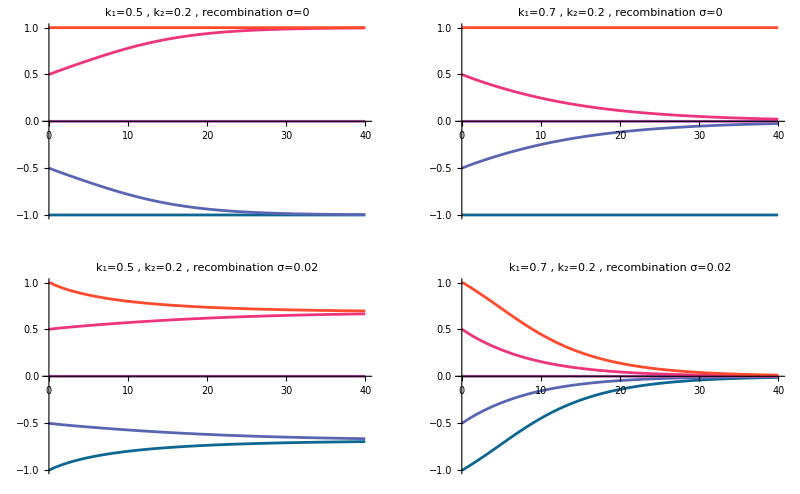

```mathematica
GraphicsGrid[{{ps1[[1]],ps2[[1]]},{ps1[[2]],ps2[[2]]}}]
```

### freq

```mathematica
frequenciesfreq[a_,b_]:={a,b};
inits = {s[0]==b /d};
initpoly=ft[{Table[Subscript[ℐ, k][0] ==0,{k,polygeno}]}];


initmonofreq[a_,b_]:=ft[Table[Subscript[ℐ, k][0] == 1 *Product[If[k[[X]]==1,frequenciesfreq[a,b][[X]],1-frequenciesfreq[a,b][[X]]], {X,divloci}]+ 0Dini If[k[[locus1]] == k[[locus2]],1,-1],{k,monogeno}]]; (*all monos + jitter*)
(*all monos + jitter*)
(*initmono={Subscript[ℐ, {0,0,0,0,0}][0]==0.4,Subscript[ℐ, {0,0,0,0,1}][0]==0.1,Subscript[ℐ, {0,0,0,1,0}][0]==0.1,Subscript[ℐ, {0,0,0,1,1}][0]==0.4};*)


initfreq[a_,b_]:={inits,initpoly,initmonofreq[a,b]}//ft;


vars = {s[t],Table[Subscript[ℐ, j][t],{j,monogeno}],Table[Subscript[ℐ, j][t],{j,polygeno}]}//ft;


solfreq[a_,b_]:=NDSolve[{eq//.params,initfreq[a,b]//.params}//ft,vars,{t,0,temps},MaxStepSize->0.1]//ft;

Do[Do[
solfreqt[a,b]=NDSolve[{eq//.params,initfreq[a,b]//.params}//ft,vars,{t,0,temps},MaxStepSize->0.1]//ft,{a,0.1,0.9,0.1}],{b,0.1,0.9,0.1}]
```

NDSolve::nderr: Error test failure at t == 1.06332; unable to continue.

NDSolve::nderr: Error test failure at t == 1.13627; unable to continue.

NDSolve::nderr: Error test failure at t == 1.06434; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

```mathematica
ps2={};
Do[frequencies={0.5,0.5};

inits = {s[0]==b /d};
initpoly=ft[{Table[Subscript[ℐ, k][0] ==0,{k,polygeno}]}];
initmonoD[Dtemp_]=ft[Table[Subscript[ℐ, k][0] == 1 *Product[If[k[[X]]==1,frequencies[[X]],1-frequencies[[X]]] , {X,divloci}]+ Dtemp If[k[[locus1]] == k[[locus2]],1,-1],{k,monogeno}]]; (*all monos + jitter*)
(*initmono={Subscript[ℐ, {0,0,0,0,0}][0]==0.4,Subscript[ℐ, {0,0,0,0,1}][0]==0.1,Subscript[ℐ, {0,0,0,1,0}][0]==0.1,Subscript[ℐ, {0,0,0,1,1}][0]==0.4};*)

initD[Dtemp_]:={inits,initpoly,initmonoD[Dtemp]}//ft;

initsol[Dtemp_]:=NDSolve[{eq//.recparams[σ0,0.7,0.2],initD[Dtemp]//.recparams[σ0,0.7,0.2]}//ft,vars,{t,0,temps},MaxStepSize->0.1]//ft;
tmax=20;
tempsol=.;
listDstart=Range[-0.25,0.25,0.125];
tempsol=ConstantArray[0,Length[listDstart]];

i=1;
Do[tempsol[[i]] = initsol[Dstart];
i=i+1
,{Dstart,listDstart}];



(*Plot[Table[DD[t]/.tempsol[[i]]/.t->x,{i,1,Length[listDstart]}],{x,0,tmax}, PlotRange->All];*)
ps2=AppendTo[ps2,Plot[Evaluate@Table[If[Evaluate[DD[t]/.tempsol[[i]]/.t->x/.params]>0,Evaluate[posDmax[t]/.tempsol[[i]]/.t->x],Evaluate[-negDmax[t]/.tempsol[[i]]/.t->x]],{i,1,Length[listDstart]}],{x,0,tmax}, PlotRange->All, PlotLabel->"D^* k1=0.7 , k2=0.2 , recombination σ="<>ToString[σ0], PlotStyle->cols]],{σ0,{0,0.02}}]
```

## k012 barcharts figure

{}

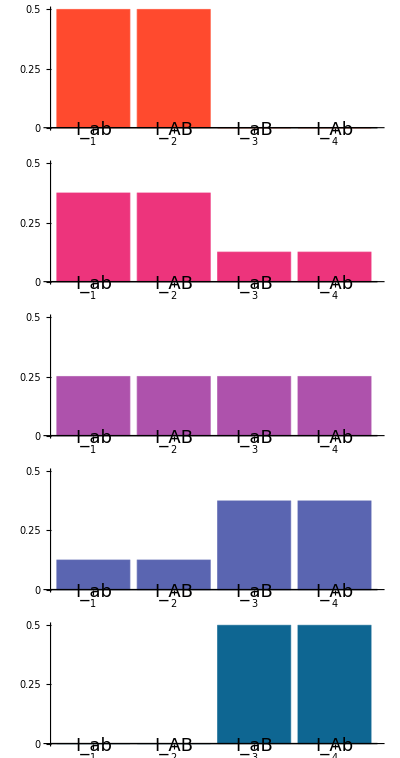

```mathematica
lblStyle=Style[#,18,Black]&;

ps3={}
Do[ps3=AppendTo[ps3,BarChart[{Subscript[ℐ, {0,0}][t]/.tempsol[[i]]/.t->0,Subscript[ℐ, {1,1}][t]/.tempsol[[i]]/.t->0,Subscript[ℐ, {0,1}][t]/.tempsol[[i]]/.t->0,Subscript[ℐ, {1,0}][t]/.tempsol[[i]]/.t->0}, ChartLabels->lblStyle/@{"I_ab","I_AB","I_aB","I_Ab"}, ChartStyle->cols[[i]], AspectRatio->1/4, PlotRange->{Automatic,{-0.0,0.5}},ImagePadding->{{25,-10},{25,10}},BarSpacing->0.1,"FixedBarSpacing"->True, Ticks->{Automatic,{0,0.25,0.5}}]],{i,1,Length[tempsol]}]
(*,Epilog->{Red,Dashed,Line[{{0,0.65},{3.55,0.65}}]},BarSpacing->0.6, AspectRatio->2
*)

GraphicsColumn[Reverse[ps3]]
```

# k0 k1 one locus

```mathematica
ClearAll["Global`*"];
ft=Flatten;
fs=FullSimplify;
mx=MatrixForm;
ff=First;



monogeno={0,1};

divloci={1};
L=Length[divloci];

locus1=1;

frequencies = 0.9;
(*monogeno={{0,0,0,0,0},{0,0,0,0,1},{1,0,0,0,0},{1,0,0,0,1}}*)

polygeno = Flatten[Table[Table[Sort[{monogeno[[i]],monogeno[[j]]}],{j,i,Length[monogeno]}],{i,1,Length[monogeno]}],1]

sig=0.0;
params = {β0->2,b->4,d->1,q->0.5,cc->1,σ->sig,γ->2,k0->1, k1->1,k2->0.6};


recparams[x_,y_,z_]:={ σ->x,k1->y, q->z ,params}//ft
```

{{0,0},{0,1},{1,1}}

β : transmission rate
b : birth rate s
d : death rate s and i
q : [0, 1] cost of infection of poly relative to mono
γ : recovery rate 
σ : recombination rate
k_i : COST upon co-colonization if allele on locus i is shared (positive: assortative ; negative : disassortative)
m : benefit of advantageous allele
cc : efficiency of co-colonization relative to primary colonization

#### all multiplicative

```mathematica
n=Length[monogeno[[1]]]; (* number of genes *)
β[i_,j_] := If[j===-1,Subscript[β, mono][i],Subscript[β, co][i,j]]
```

```mathematica
Subscript[β, mono][i_] := β0 
Subscript[β, co][i_,j_]:=cc (β0 * Subscript[K, metabo][i,j])  (*i infects already j*)


Subscript[K, metabo][i_,j_] :=  If[i==j,k1,k0]





sort[i_,j_]:= Sort[{i,j}]  (* to insure that using Subscript[i, i,j] is the same is Subscript[i, j,i]*)


δsame[i_,j_] := If[i==j,1,0]

(*Subscript[p, rec][i_,j_,l_] :=Sum[If[ (Delete[i,X]== Delete[l,X]) && j[[X]]==l[[X]],1/n,0],{X,1,n}]*) (* proba that i recombines with j to form l*) (*for now recombination of i with j gives : i but at one random position (all equally likely) its the allele of j*)    (*BENEF UNABLE TO RECOMBINE*)
Subscript[p, rec][i_,j_,l_] :=0

irec[i_,j_,X_]:=ReplacePart[i,X->j[[X]]]
```

```mathematica
monogeno
```

{0,1}

```mathematica
β[0,0]
β[1,0]
β[0,0]
β[1,1]
```

cc k1 β0

cc k0 β0

cc k1 β0

cc k1 β0

```mathematica
eqmono=Table[Subscript[ℐ, i]'[t] == (β[i,-1]  Subscript[ℐ, i][t])s[t]  (* + mono infects s*)

- Subscript[ℐ, i][t](d+γ)(* - death+recovery*)

-Subscript[ℐ, i][t] Sum[ (Subscript[ℐ, j][t]  β[j,i]),{j,monogeno}](* - mono infects mono*)

+ γ( Sum[Subscript[ℐ, sort[i,j]][t] ,{j,monogeno}] + Subscript[ℐ, sort[i,i]][t])(* + recovery of poly*)

+ s[t](1-σ) Sum[Subscript[ℐ, sort[i,j]][t] β[i,-1] q (1+δsame[i,j]),{j,monogeno}] (*poly infects s*) (* no recombi*)

-  Subscript[ℐ, i][t] q (1-σ)Sum[Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t] (β[ij[[1]],i]+β[ij[[2]],i]),{ij,polygeno}] (* - poly infects mono*) (* no recombi*)

-  Subscript[ℐ, i][t] q σ Sum[1/L Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t]  β[irec[lm[[1]],lm[[2]],nrec],i] +  Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t]  β[irec[lm[[2]],lm[[1]],nrec],i] ,{nrec,divloci}],{lm,polygeno}] (* - poly infects mono*) (* RECOMBI*)

+ σ s[t] β[i,-1] q Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t] (Subscript[p, rec][lm[[1]],lm[[2]],i]+Subscript[p, rec][lm[[2]],lm[[1]],i]),{lm,polygeno}](*poly infects s*) (* recombi*)


,{i,monogeno}];


eqpoly = Table[Subscript[ℐ, sort[ij[[1]],ij[[2]]]]'[t] ==  Subscript[ℐ, ij[[1]]][t]  Subscript[ℐ, ij[[2]]][t](β[ij[[1]],ij[[2]]] +( 1-δsame[ij[[1]],ij[[2]]]) β[ij[[2]],ij[[1]]])(* + mono infects mono *) 
   
- Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t](d+2γ)(* - death+recovery *)

+Subscript[ℐ, ij[[1]]][t] q  (1-σ)Sum[Subscript[ℐ, sort[ij[[2]],l]][t] β[ij[[2]],ij[[1]]] (1+δsame[ij[[2]],l]),{l,monogeno}] (*poly infects mono1*) (* no recombi*)

+(1-δsame[ij[[1]],ij[[2]]])Subscript[ℐ, ij[[2]]][t] q  (1-σ)Sum[Subscript[ℐ, sort[ij[[1]],l]][t] β[ij[[1]],ij[[2]]] (1+δsame[ij[[1]],l]),{l,monogeno}] (*poly infects mono2 if not same *)(* no recombi*)

+Subscript[ℐ, ij[[1]]][t] q  σ Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t] β[ij[[2]],ij[[1]]]  (Subscript[p, rec][lm[[1]],lm[[2]],ij[[2]]] + Subscript[p, rec][lm[[2]],lm[[1]],ij[[2]]]),{lm,polygeno}] (*poly infects mono1*) (* RECOMBI*)

+(1-δsame[ij[[1]],ij[[2]]])Subscript[ℐ, ij[[2]]][t] q  σ Sum[Subscript[ℐ, sort[lm[[1]],lm[[2]]]][t] β[ij[[1]],ij[[2]]]  (Subscript[p, rec][lm[[1]],lm[[2]],ij[[1]]] + Subscript[p, rec][lm[[2]],lm[[1]],ij[[1]]]),{lm,polygeno}] (*poly infects mono1*) (* RECOMBI*)

,{ij,polygeno}];




eqs=s'[t]==b (* + birth*)   -s[t] (Sum[Subscript[ℐ, j][t] β[j,-1],{j,monogeno}]) (* - mono infects s*) - s[t]d  (* - death*)  + γ (Sum[Subscript[ℐ, j][t],{j,monogeno}])  (* + recovery of mono *)- s[t] (1-σ) Sum[Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t] q (β[ij[[1]],-1] + β[ij[[2]],-1]),{ij,polygeno}] (* - poly infects s*) (*no recombi*)- s[t] σ 1/L Sum[Subscript[ℐ, sort[ij[[1]],ij[[2]]]][t] q Sum[β[irec[ij[[1]],ij[[2]],X],-1] +β[irec[ij[[2]],ij[[1]],X],-1] ,{X,divloci}],{ij,polygeno}] (* - poly infects s*) (*recombi*);




eq=  {eqs,eqmono,eqpoly}/.σ->0/.cc->1//ft


Total[eq[[All,2]]]- b+d(s[t]+Sum[Subscript[ℐ, j][t],{j,monogeno}]+Sum[Subscript[ℐ, j][t],{j,polygeno}])//fs    (*THE ABOVE TAKES A REALLY LONG TIME, USED TO CHECK IF SYSTEM IS GOOD. ONE CAN CHECK WITH THREE LOCI IN UNDER A MINUTE*)
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{s'[t]==b-d s[t]+γ (ℐ_0[t]+ℐ_1[t])-s[t] (β0 ℐ_0[t]+β0 ℐ_1[t])-s[t] (2 q β0 ℐ_{0,0}[t]+2 q β0 ℐ_{0,1}[t]+2 q β0 ℐ_{1,1}[t]),ℐ_0'[t]==-((d+γ) ℐ_0[t])+β0 s[t] ℐ_0[t]-ℐ_0[t] (k1 β0 ℐ_0[t]+k0 β0 ℐ_1[t])+γ (2 ℐ_{0,0}[t]+ℐ_{0,1}[t])+s[t] (2 q β0 ℐ_{0,0}[t]+q β0 ℐ_{0,1}[t])-q ℐ_0[t] (2 k1 β0 ℐ_{0,0}[t]+(k0 β0+k1 β0) ℐ_{0,1}[t]+2 k0 β0 ℐ_{1,1}[t]),ℐ_1'[t]==-((d+γ) ℐ_1[t])+β0 s[t] ℐ_1[t]-ℐ_1[t] (k0 β0 ℐ_0[t]+k1 β0 ℐ_1[t])+γ (ℐ_{0,1}[t]+2 ℐ_{1,1}[t])-q ℐ_1[t] (2 k0 β0 ℐ_{0,0}[t]+(k0 β0+k1 β0) ℐ_{0,1}[t]+2 k1 β0 ℐ_{1,1}[t])+s[t] (q β0 ℐ_{0,1}[t]+2 q β0 ℐ_{1,1}[t]),ℐ_{0,0}'[t]==k1 β0 ℐ_0[t]^2-(d+2 γ) ℐ_{0,0}[t]+q ℐ_0[t] (2 k1 β0 ℐ_{0,0}[t]+k1 β0 ℐ_{0,1}[t]),ℐ_{0,1}'[t]==2 k0 β0 ℐ_0[t] ℐ_1[t]-(d+2 γ) ℐ_{0,1}[t]+q ℐ_1[t] (2 k0 β0 ℐ_{0,0}[t]+k0 β0 ℐ_{0,1}[t])+q ℐ_0[t] (k0 β0 ℐ_{0,1}[t]+2 k0 β0 ℐ_{1,1}[t]),ℐ_{1,1}'[t]==k1 β0 ℐ_1[t]^2-(d+2 γ) ℐ_{1,1}[t]+q ℐ_1[t] (k1 β0 ℐ_{0,1}[t]+2 k1 β0 ℐ_{1,1}[t])}

0

```mathematica
eqrep =Thread[eq[[All,1]]->eq[[All,2]]];
D[(Subscript[ℐ, 1][t] +2 Subscript[ℐ, {1,1}][t]+Subscript[ℐ, sort[1,0]][t]) / (Subscript[ℐ, 1][t]+Subscript[ℐ, 0][t] +2 Subscript[ℐ, {1,1}][t]+2 Subscript[ℐ, {0,0}][t]+2 Subscript[ℐ, sort[1,0]][t]),t]/.eqrep/.q->1 //fs

D[(Subscript[ℐ, 1][t] +2 Subscript[ℐ, {1,1}][t]+Subscript[ℐ, sort[1,0]][t]),t]/(Subscript[ℐ, 1][t] +2 Subscript[ℐ, {1,1}][t]+Subscript[ℐ, sort[1,0]][t]) - D[(Subscript[ℐ, 0][t] +2 Subscript[ℐ, {0,0}][t]+Subscript[ℐ, sort[1,0]][t]),t]/(Subscript[ℐ, 0][t] +2 Subscript[ℐ, {0,0}][t]+Subscript[ℐ, sort[1,0]][t])/.eqrep /.q->1 //fs

D[(Subscript[ℐ, 1][t] +2 Subscript[ℐ, {1,1}][t]+Subscript[ℐ, sort[1,0]][t]) / (Subscript[ℐ, 1][t]+Subscript[ℐ, 0][t] +2 Subscript[ℐ, {1,1}][t]+2 Subscript[ℐ, {0,0}][t]+2 Subscript[ℐ, sort[1,0]][t]),t] + D[(Subscript[ℐ, 0][t] +2 Subscript[ℐ, {0,0}][t]+Subscript[ℐ, sort[1,0]][t]) / (Subscript[ℐ, 1][t]+Subscript[ℐ, 0][t] +2 Subscript[ℐ, {1,1}][t]+2 Subscript[ℐ, {0,0}][t]+2 Subscript[ℐ, sort[1,0]][t]),t] /.eqrep //fs
```

((k0-k1) β0 (ℐ_0[t]-ℐ_1[t]) (ℐ_0[t]+2 ℐ_{0,0}[t]+ℐ_{0,1}[t]) (ℐ_1[t]+ℐ_{0,1}[t]+2 ℐ_{1,1}[t]))/(ℐ_0[t]+ℐ_1[t]+2 (ℐ_{0,0}[t]+ℐ_{0,1}[t]+ℐ_{1,1}[t]))^2

(k0-k1) β0 (ℐ_0[t]-ℐ_1[t])

0

```mathematica
temps=10000;



inits = {s[0]==b /d};
initpoly=ft[{Table[Subscript[ℐ, k][0] ==0,{k,polygeno}]}];


initmono=ft[Table[Subscript[ℐ, k][0] == 1 *If[k==1,frequencies,1-frequencies],{k,monogeno}]]; (*all monos + jitter*)

(*initmono={Subscript[ℐ, {0,0,0,0,0}][0]==0.4,Subscript[ℐ, {0,0,0,0,1}][0]==0.1,Subscript[ℐ, {0,0,0,1,0}][0]==0.1,Subscript[ℐ, {0,0,0,1,1}][0]==0.4};*)


init={inits,initpoly,initmono}//ft


vars = {s[t],Table[Subscript[ℐ, j][t],{j,monogeno}],Table[Subscript[ℐ, j][t],{j,polygeno}]}//ft;


sol=NDSolve[{eq//.params,init//.params}//ft,vars,{t,0,temps},MaxStepSize->0.1];

(*Plot[Subscript[ℐ, {0,0,0,0,0}][t]/.sol,{t,0,temps}, PlotRange->All];*)

recsol[x_,y_,z_]:=NDSolve[{eq//.recparams[x,y,z],init//.recparams[x,y,z]}//ft,vars,{t,0,temps},MaxStepSize->0.1];
```

{s[0]==b/d,ℐ_{0,0}[0]==0,ℐ_{0,1}[0]==0,ℐ_{1,1}[0]==0,ℐ_0[0]==0.1,ℐ_1[0]==0.9}

```mathematica
init//.params
```

{s[0]==4,ℐ_{0,0}[0]==0,ℐ_{0,1}[0]==0,ℐ_{1,1}[0]==0,ℐ_0[0]==0.1,ℐ_1[0]==0.9}

heatmap for presence in co - colonisation

in the whole pop

```mathematica
eqth=Thread[eq[[All,1]]->eq[[All,2]]];
```

```mathematica
denstot[t_]= Sum[(Subscript[ℐ, x][t]),{x,monogeno}]+ 2Sum[(Subscript[ℐ, x][t]),{x,polygeno}];

Subscript[dens, A][t_]=Subscript[ℐ, 1][t] +Subscript[ℐ, {0,1}][t]+2 Subscript[ℐ, {1,1}][t] ;

Subscript[dens, a][t_]=Subscript[ℐ, 0][t] +Subscript[ℐ, {0,1}][t]+2 Subscript[ℐ, {0,0}][t] ;

Subscript[fgene, A][t_] =Subscript[dens, A][t]/denstot[t];

Subscript[feff, A][t] = (Subscript[ℐ, 1][t] +2 q Subscript[ℐ, {1,1}][t]+q Subscript[ℐ, sort[1,0]][t]) / (Subscript[ℐ, 1][t]+Subscript[ℐ, 0][t] +2q Subscript[ℐ, {1,1}][t]+2 q Subscript[ℐ, {0,0}][t]+2q Subscript[ℐ, sort[1,0]][t]);


Subscript[Dfgene, A][t_]=Evaluate[D[Subscript[fgene, A][t],t]]/.eqth;

Subscript[r, a][t_] = D[Subscript[dens, a][t],t] / Subscript[dens, a][t];
Subscript[r, A][t_] = D[Subscript[dens, A][t],t] / Subscript[dens, A][t];

Subscript[s, A][t_] =Subscript[r, A][t]-Subscript[r, a][t];
```

```mathematica
D[Subscript[feff, A][t],t]/.eqth/.q->(1/2)//fs
D[Subscript[feff, A][t],t]/.eqth/.q->0.5//fs

Subscript[s, A][t]/.eqth/.q->(1/2)//fs
Subscript[s, A][t]/.eqth/.q->1//fs
Subscript[s, A][t]/.eqth/.q->0//fs
Subscript[s, A][t]/.eqth//fs
```

((2 γ+k0 β0 (ℐ_0[t]+ℐ_1[t]+ℐ_{0,0}[t]+ℐ_{0,1}[t]+ℐ_{1,1}[t])) (-ℐ_1[t] (2 ℐ_{0,0}[t]+ℐ_{0,1}[t])+ℐ_0[t] (ℐ_{0,1}[t]+2 ℐ_{1,1}[t])))/(4 (ℐ_0[t]+ℐ_1[t]+ℐ_{0,0}[t]+ℐ_{0,1}[t]+ℐ_{1,1}[t])^2)

0.5 k0 β0 ℐ_0[t]+(0.-1. γ ℐ_0[t]^2+γ ℐ_1[t] (-1. ℐ_{0,0}[t]-0.5 ℐ_{0,1}[t])+γ ℐ_0[t] (-1. ℐ_1[t]-1. ℐ_{0,0}[t]-0.5 ℐ_{0,1}[t]))/(1. ℐ_0[t]+1. ℐ_1[t]+1. ℐ_{0,0}[t]+1. ℐ_{0,1}[t]+1. ℐ_{1,1}[t])^2+(-0.5 k0 β0 ℐ_0[t]^2+ℐ_0[t] (1. γ+k0 β0 (-0.5 ℐ_1[t]-0.5 ℐ_{0,0}[t]-0.25 ℐ_{0,1}[t]))+k0 β0 ℐ_1[t] (-0.5 ℐ_{0,0}[t]-0.25 ℐ_{0,1}[t]))/(1. ℐ_0[t]+1. ℐ_1[t]+1. ℐ_{0,0}[t]+1. ℐ_{0,1}[t]+1. ℐ_{1,1}[t])

1/2 β0 ((k0-k1) (ℐ_0[t]-ℐ_1[t])-(ℐ_0[t] (s[t]+k1 ℐ_0[t]+k0 ℐ_1[t]))/(ℐ_0[t]+2 ℐ_{0,0}[t]+ℐ_{0,1}[t])+(ℐ_1[t] (s[t]+k0 ℐ_0[t]+k1 ℐ_1[t]))/(ℐ_1[t]+ℐ_{0,1}[t]+2 ℐ_{1,1}[t]))

(k0-k1) β0 (ℐ_0[t]-ℐ_1[t])

-(β0 ℐ_0[t] (s[t]+k1 ℐ_0[t]+k0 ℐ_1[t]))/(ℐ_0[t]+2 ℐ_{0,0}[t]+ℐ_{0,1}[t])+(β0 ℐ_1[t] (s[t]+k0 ℐ_0[t]+k1 ℐ_1[t]))/(ℐ_1[t]+ℐ_{0,1}[t]+2 ℐ_{1,1}[t])

(β0 (ℐ_1[t] (2 ℐ_{0,0}[t]+ℐ_{0,1}[t]) (-((-1+q) s[t])+(k1-k0 q) ℐ_1[t]-(k0-k1) q (ℐ_{0,1}[t]+2 ℐ_{1,1}[t]))+ℐ_0[t]^2 ((k0-k1) ℐ_1[t]-(k1-k0 q) (ℐ_{0,1}[t]+2 ℐ_{1,1}[t]))+ℐ_0[t] ((-k0+k1) ℐ_1[t]^2+2 (k0-k1 q) ℐ_1[t] (ℐ_{0,0}[t]-ℐ_{1,1}[t])+((-1+q) s[t]+(k0-k1) q (2 ℐ_{0,0}[t]+ℐ_{0,1}[t])) (ℐ_{0,1}[t]+2 ℐ_{1,1}[t]))))/((ℐ_0[t]+2 ℐ_{0,0}[t]+ℐ_{0,1}[t]) (ℐ_1[t]+ℐ_{0,1}[t]+2 ℐ_{1,1}[t]))

```mathematica
tmax=temps


kmin=0
kmax=1
kstep=0.02

transpa=ListPlot[{{0,0},{1,1}}, Filling->Bottom,Joined->True, FillingStyle->Opacity[1,White], PlotStyle->Opacity[0.5,Gray]];
```

10000

0

1

0.02

## Figure S2

```mathematica
rainbow[z_]:=Blend[{RGBColor["#3C4ABA"],
RGBColor["#A6BEFA"],
RGBColor["#DEDEDE"],
RGBColor["#ECB295"],
RGBColor["#A62129"]},z];
col[v_]=Opacity[0.7,rainbow[Rescale[v,{-01,1}]]];

line=Graphics[Line[{{0.,0.5},{1,1}}]];

(*Table[Table[Print[ListDensityPlot[Table[
DD[t]/.recsol[tempσ,k1,k2,Dtemp]/.t->tmax//ft//ff
,{k1,kmin,kmax,kstep},{k2,kmin,kmax,kstep}],DataRange->{{0,kmax},{0,kmax}}, FrameLabel->{"k2","k1"}, PlotLegends->Automatic,PlotLabel->"recombination σ ="<>ToString[tempσ] ,
 PlotLegends->BarLegend[{rainbow[Rescale[#1,{-6,4}]]&,{1,4}}],
ColorFunctionScaling->False, 
ColorFunction->col    ]],{tempσ,tempσs}],{Dtemp,Dtemps}]*)


transpa=ListPlot[{{0,0},{1,1}}, Filling->Bottom,Joined->True, FillingStyle->Opacity[1,White], PlotStyle->Opacity[0.5,Gray]];

(*Show[ListDensityPlot[Replace[Table[
If[(DD[t]/.recsol[0,1,k2]/.t->tmax//ft//ff)>=0,posDmax[t]/.recsol[0,1,k2]/.t->tmax//ft//ff,-negDmax[t]/.recsol[0,1,k2]/.t->tmax//ft//ff]/.Indeterminate->0/.ComplexInfinity->0
,{k1,kmin,kmax,kstep},{k2,kmin,kmax,kstep}],x_?NumericQ:>If[Abs[x]>10,0,x],{2}],DataRange->{{0,kmax},{0,kmax}}, PlotLegends->Automatic,PlotLabel->"recombination σ ="<>ToString[tempσ] ,
 PlotLegends->BarLegend[{rainbow[Rescale[#1,{-6,4}]]&,{1,4}}],
ColorFunctionScaling->False, 
ColorFunction->col    , Frame->{{True,False},{False,True}}, PlotRangePadding->None, FrameLabel->{{Style["k_1",14, Black],None},{None,Style["k_2",14, Black]}},FrameTicks->{{Automatic,None},{None,All}}],transpa,line]*)


ListDensityPlot[Table[
Subscript[fgene, A][t]/.recsol[0,k1,q]/.t->tmax//ft//ff ,{k1,kmin,kmax,kstep},{q,kmin,kmax,kstep}],DataRange->{{0,kmax},{0,kmax}}, PlotLegends->Automatic,PlotLabel->"recombination σ ="<>ToString[tempσ] ,
 PlotLegends->BarLegend[{rainbow[Rescale[#1,{-6,4}]]&,{1,4}}],
ColorFunctionScaling->False, 
ColorFunction->col    , Frame->{{True,False},{False,True}}, PlotRangePadding->None, FrameLabel->{{Style["k_1",14, Black],None},{None,Style["q",14, Black]}},FrameTicks->{{Automatic,None},{None,All}}]
```

Blend::argl: 1/2+v/2 should be a real number or a list of non-negative numbers, which has the same length as {color,color,color,color,color}.

-Graphics-